```mathematica
S :=16
S
Sc := S/2
```

16

```mathematica
cr:={{0,1},{0,0}}
```

```mathematica
an:= {{0,0},{1,0}}
n=.
```

```mathematica
cr ;
```

```mathematica
an ;
```

```mathematica
id2 := {{-1,0},{0,1}}
```

```mathematica
id := IdentityMatrix[2]
```

```mathematica
c[n_]:=SparseArray[KroneckerProduct@@( Table[id,(n-1)]~Join~{cr}~Join~Table[id2,{Sc-n}])]
cd[n_]:=SparseArray[KroneckerProduct@@(Table[id,(n-1)]~Join~{an}~Join~Table[id2,{Sc-n}])]
```

```mathematica
c[1].cd[1] +cd[1].c[1] ;
```

```mathematica
Do[ψ[n] =  (1/Sqrt[2]) *(c[n] + cd[n]),{n,Sc}]
```

```mathematica
Do[ψ[Sc +n] = ( 1/Sqrt[2]) *(-I*c[n] + I*cd[n]),{n,Sc}]
```

```mathematica
Do[ψ[i1,i2] = ψ[i1].ψ[i2],{i1,S},{i2,S}] //Timing
Do[ψ[i3,i4] = ψ[i3].ψ[i4],{i3,S},{i4,S}]
```

{0.048712,Null}

Hamiltonian q = 2

```mathematica
ψ[1,1] ;
q = 2;
J = 1;
```

```mathematica
Js =RandomVariate[NormalDistribution[0,Sqrt[ (J^2)*  (   (q-1)! /  (S^(q-1))  ) ]],{S,S}]
```

{{-0.0489194,-0.224879,0.0187036,-0.371167,-0.138508,0.395436,-0.44221,-0.457569,-0.2664,-0.363714,-0.531623,-0.205805,0.0795659,0.282232,0.126332,0.465541},{-0.200289,-0.00435953,-0.431903,0.0189042,-0.0855657,-0.430771,0.112109,-0.152356,-0.273491,0.00651877,-0.085554,-0.192404,-0.096431,0.15297,0.0070294,-1.06287},{-0.255307,0.033957,0.0759824,0.0320758,0.0962582,0.370996,0.107507,0.0687588,-0.0839152,0.433298,-0.356612,0.403281,0.135204,0.437046,-0.334126,0.0829714},{0.430137,0.444869,-0.0744296,-0.402576,0.0986474,-0.00408623,0.0970411,0.301268,-0.0308262,0.134501,-0.107024,-0.387914,0.0474704,-0.0317709,0.00790474,-0.0814116},{0.0518719,-0.344281,0.0845449,0.230998,0.262122,0.370759,-0.025712,-0.164649,-0.0452081,-0.130557,0.210295,0.355222,-0.147962,-0.0257641,0.18679,0.0255095},{-0.0656935,0.169862,-0.174865,0.134809,0.0998637,0.235993,0.203056,0.150366,-0.275852,0.632073,-0.314667,-0.197691,0.176283,-0.143823,0.0197202,0.157545},{0.264084,0.274682,0.112717,0.0977801,-0.0127269,-0.409067,0.150623,-0.0827522,0.0333648,-0.122857,-0.400112,0.00978636,0.0913825,0.623874,0.221513,0.105811},{0.0791087,-0.324637,-0.381881,0.349991,-0.235657,-0.145257,0.272524,0.204774,0.192138,-0.15918,-0.0277359,-0.189252,-0.309301,-0.28628,0.0754534,0.209504},{-0.440218,-0.05193,-0.016513,-0.356275,0.292087,-0.222934,0.134252,0.145083,-0.314893,-0.106409,0.0153258,-0.112823,-0.404042,-0.0814831,0.0955721,0.109544},{-0.488301,-0.32397,-0.11593,0.130338,-0.0327356,-0.634696,-0.158616,-0.477979,0.173413,-0.356227,-0.127181,0.102639,-0.278777,0.277286,-0.409001,-0.20749},{0.06026,0.418725,-0.0835344,0.160769,-0.169849,0.0221477,0.00228497,-0.235567,-0.0488625,0.00827652,0.104685,-0.499306,0.144849,-0.000226318,0.0268021,-0.0174341},{0.363205,-0.125351,0.0490961,-0.326095,-0.104901,-0.219652,0.244861,-0.141203,0.223259,-0.0666131,0.0562673,0.0776461,-0.47226,0.126234,0.0475763,-0.00703472},{-0.0535108,-0.108836,-0.251072,-0.18953,0.199074,-0.411943,-0.45982,-0.152635,-0.181599,-0.079928,-0.61038,-0.0708233,0.254521,0.14149,-0.204024,0.164644},{-0.176319,-0.0375434,-0.00819487,-0.153621,0.0195032,-0.361097,-0.323413,-0.202394,-0.100857,0.113418,-0.242055,-0.481977,0.21348,-0.323273,-0.405068,-0.275863},{0.0208431,-0.0864243,-0.12985,0.110045,0.0952625,-0.0558473,-0.0892359,-0.414265,-0.0475589,-0.137744,-0.322507,0.037335,-0.152465,0.0953758,-0.417748,-0.518968},{-0.164533,-0.140917,-0.393414,0.0302401,-0.304285,-0.234782,-0.0541714,-0.00559783,-0.233323,-0.0828849,-0.424313,0.527539,-0.0207522,0.121031,0.110824,0.0455267}}

```mathematica
H=Sum[I* Js[[i1,i2]]*ψ[i1,i2],{i1,S},{i2,i1+1,S}]//Normal;
```

```mathematica
iv =H//N//Eigenvalues//Sort
```

{-3.39148,-3.38928,-3.18396,-3.18177,-2.98707,-2.98487,-2.77956,-2.77736,-2.70626,-2.70407,-2.49875,-2.49655,-2.36258,-2.36039,-2.30185,-2.29966,-2.15507,-2.15288,-2.09434,-2.09215,-2.09191,-2.08971,-1.95858,-1.95818,-1.95638,-1.95598,-1.8844,-1.8822,-1.75107,-1.75066,-1.74887,-1.74847,-1.6875,-1.6853,-1.67737,-1.67517,-1.66921,-1.66701,-1.55417,-1.55197,-1.47999,-1.47779,-1.46986,-1.46766,-1.4617,-1.4595,-1.40669,-1.4045,-1.34666,-1.34446,-1.27337,-1.27296,-1.27117,-1.27077,-1.2648,-1.2626,-1.19918,-1.19699,-1.06586,-1.06545,-1.06366,-1.06325,-1.06302,-1.06082,-1.05729,-1.05509,-1.00228,-1.00009,-0.983993,-0.981797,-0.929689,-0.927493,-0.868957,-0.86676,-0.855507,-0.853311,-0.794774,-0.792578,-0.776483,-0.774287,-0.722179,-0.719983,-0.661446,-0.65925,-0.659013,-0.658608,-0.656817,-0.656412,-0.640317,-0.638121,-0.579584,-0.577388,-0.52528,-0.523084,-0.451502,-0.451098,-0.449306,-0.448902,-0.432806,-0.43061,-0.377804,-0.375608,-0.372074,-0.369878,-0.369641,-0.367444,-0.31777,-0.315573,-0.254604,-0.252408,-0.244475,-0.242279,-0.236312,-0.235908,-0.234116,-0.233711,-0.170293,-0.168097,-0.16213,-0.159934,-0.0470932,-0.0448971,-0.0369649,-0.0347688,-0.0288017,-0.0283971,-0.0266056,-0.026201,0.026201,0.0266056,0.0283971,0.0288017,0.0347688,0.0369649,0.0448971,0.0470932,0.159934,0.16213,0.168097,0.170293,0.233711,0.234116,0.235908,0.236312,0.242279,0.244475,0.252408,0.254604,0.315573,0.31777,0.367444,0.369641,0.369878,0.372074,0.375608,0.377804,0.43061,0.432806,0.448902,0.449306,0.451098,0.451502,0.523084,0.52528,0.577388,0.579584,0.638121,0.640317,0.656412,0.656817,0.658608,0.659013,0.65925,0.661446,0.719983,0.722179,0.774287,0.776483,0.792578,0.794774,0.853311,0.855507,0.86676,0.868957,0.927493,0.929689,0.981797,0.983993,1.00009,1.00228,1.05509,1.05729,1.06082,1.06302,1.06325,1.06366,1.06545,1.06586,1.19699,1.19918,1.2626,1.2648,1.27077,1.27117,1.27296,1.27337,1.34446,1.34666,1.4045,1.40669,1.4595,1.4617,1.46766,1.46986,1.47779,1.47999,1.55197,1.55417,1.66701,1.66921,1.67517,1.67737,1.6853,1.6875,1.74847,1.74887,1.75066,1.75107,1.8822,1.8844,1.95598,1.95638,1.95818,1.95858,2.08971,2.09191,2.09215,2.09434,2.15288,2.15507,2.29966,2.30185,2.36039,2.36258,2.49655,2.49875,2.70407,2.70626,2.77736,2.77956,2.98487,2.98707,3.18177,3.18396,3.38928,3.39148}

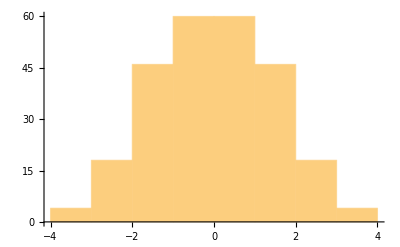

```mathematica
Histogram[iv]
```

```mathematica
q=4
```

4

```mathematica
J=4
```

4

```mathematica
Jm =RandomVariate[NormalDistribution[0,Sqrt[J^2   * ((q-1)!)/(S^(q-1))]],{S,S,S,S}]
```

```mathematica
Dynamic[{i1,i2,i3,i4}]
Ham=I^(q/2)Sum[ψ[i1,i2].Sum[ Jm[[i1,i2,i3,i4]]*ψ[i3,i4],{i3,i2+1,S},{i4,i3 + 1, S}],{i1,S-3},{i2,i1 + 1, S-2}]//Normal;
```

```mathematica
Ham
```

```mathematica
ivv = Ham//N//Eigenvalues//Sort
```

{-3.21233,-3.08829,-3.07375,-3.06042,-2.9987,-2.89827,-2.87913,-2.83403,-2.80051,-2.78411,-2.74937,-2.71505,-2.67304,-2.61593,-2.58706,-2.58142,-2.52445,-2.51733,-2.50804,-2.48329,-2.42984,-2.40835,-2.39037,-2.3651,-2.36134,-2.26887,-2.19966,-2.18963,-2.16794,-2.1514,-2.14808,-2.12688,-2.07957,-2.07051,-2.05201,-2.04743,-2.01189,-1.95527,-1.95027,-1.93067,-1.89424,-1.8942,-1.85561,-1.83701,-1.83336,-1.76759,-1.76375,-1.7418,-1.69618,-1.67686,-1.65411,-1.64343,-1.63567,-1.55338,-1.55257,-1.52002,-1.51695,-1.4792,-1.45234,-1.45163,-1.40489,-1.40405,-1.37218,-1.36119,-1.33217,-1.32422,-1.30439,-1.29474,-1.24979,-1.24898,-1.22571,-1.20189,-1.19345,-1.15205,-1.10406,-1.084,-1.0795,-1.04143,-1.01209,-0.984516,-0.97921,-0.952279,-0.926971,-0.913277,-0.890661,-0.86754,-0.853716,-0.809956,-0.787521,-0.769042,-0.761224,-0.716052,-0.708551,-0.70548,-0.675971,-0.657549,-0.626881,-0.620124,-0.597331,-0.577691,-0.552121,-0.54648,-0.52139,-0.509553,-0.494865,-0.462701,-0.44388,-0.435027,-0.400474,-0.371482,-0.358241,-0.357532,-0.327205,-0.313993,-0.299741,-0.295283,-0.262896,-0.217802,-0.193863,-0.158334,-0.140936,-0.137372,-0.122543,-0.0956337,-0.0263718,-0.0214707,0.00813232,0.0330346,0.0340849,0.0430188,0.0670332,0.105804,0.112833,0.137231,0.143766,0.154109,0.159944,0.198722,0.206839,0.230006,0.243736,0.26967,0.282236,0.302709,0.360966,0.382921,0.388692,0.430904,0.453356,0.457936,0.48219,0.491209,0.504015,0.565988,0.582025,0.598986,0.608317,0.628272,0.641153,0.65517,0.666712,0.666775,0.722737,0.72685,0.752958,0.759231,0.779113,0.805397,0.836041,0.865141,0.883394,0.899028,0.912422,0.947885,0.959043,0.978537,0.990601,1.04413,1.06143,1.09378,1.0984,1.10659,1.13226,1.1417,1.18243,1.19204,1.24452,1.2634,1.27539,1.30095,1.33003,1.35138,1.37223,1.39767,1.39822,1.43579,1.46356,1.46447,1.4879,1.4928,1.51247,1.5661,1.5781,1.61671,1.61847,1.64115,1.65858,1.66834,1.73865,1.76497,1.77349,1.80103,1.81176,1.85468,1.86367,1.89066,1.9256,1.93301,1.93721,2.04245,2.04973,2.0498,2.06102,2.06569,2.11002,2.12824,2.15812,2.18198,2.21311,2.21737,2.23145,2.27701,2.31199,2.33234,2.38011,2.38741,2.39525,2.43501,2.47927,2.52817,2.60369,2.60481,2.63194,2.64268,2.7003,2.73598,2.78332,2.78944,2.80859,2.84669,2.9252,2.97259,3.06176,3.09391,3.14191,3.16807}

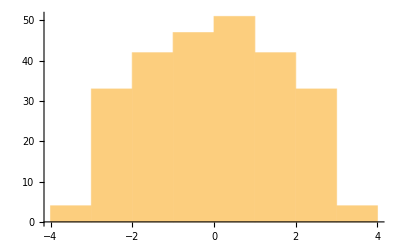

```mathematica
ivv //Histogram
```

Two Point functions

```mathematica
β =5;
H = Ham //N
```

```mathematica
Clear[Gn];
Gn[a_,b_,τ_,β_, λ_]:=Gn[a,b,τ,β ,λ]= Block[{ },
If[τ>0,
Eτ = MatrixExp[-τ H  λ ];
Eβτ = MatrixExp[(-β + τ) H λ];
(Tr[Eβτ.ψ[a].Eτ.ψ[b]]) / (Tr[Eβτ.Eτ]),

Eτ = MatrixExp[+τ H λ];
Eβτ = MatrixExp[(-β - τ) H λ];
-(Tr[Eβτ.ψ[b].Eτ.ψ[a]]) / (Tr[Eβτ.Eτ]),
]
]
```

```mathematica
Gn[1,1,1/4,1,1]
```

0.413257-2.48759×10^-19 ⅈ

```mathematica
Dynamic[tt]
Gn[1,1,1,1,1]
```

0.5+9.62965×10^-34 ⅈ

```mathematica
tbGG =Table[{tt,Gn[1,1,tt,1,1]},{tt,-1/2,1/2,1/10}]//Re
```

{{-1/2,-0.388634},{-2/5,-0.392445},{-3/10,-0.404169},{-1/5,-0.424723},{-1/10,-0.455777},{0,-0.5},{1/10,0.455777},{1/5,0.424723},{3/10,0.404169},{2/5,0.392445},{1/2,0.388634}}

```mathematica
plt = ListPlot[tbGG,Joined->True]
```

-Graphics-

```mathematica
Spec[τ_,β_]:=Spec[τ,β ]= Block[{ },
If[τ>0,
Zβτ = Tr[MatrixExp[(-β *H)  -( I* H* τ)]];
Zβ = Tr[MatrixExp[(-β * H )]];
Abs[(Zβτ/Zβ )]^2
]
]
```

```mathematica
Spec[3,1]
```

0.0464621

```mathematica
tbSpec =Table[{tt,Spec[tt,1]},{tt,1,100,1}]//Re
```

{{1,0.426558},{2,0.123482},{3,0.0464621},{4,0.0205906},{5,0.0125959},{6,0.00697112},{7,0.00423197},{8,0.00266093},{9,0.0000779763},{10,0.0037585},{11,0.00651388},{12,0.00629446},{13,0.00206251},{14,0.00154685},{15,0.0000798716},{16,0.00153077},{17,0.00748674},{18,0.0107484},{19,0.0107598},{20,0.0122338},{21,0.01131},{22,0.00581723},{23,0.00201071},{24,0.00130226},{25,0.00363828},{26,0.00784598},{27,0.0164146},{28,0.0175225},{29,0.0110508},{30,0.00467426},{31,0.00123695},{32,0.00282228},{33,0.00174583},{34,0.005009},{35,0.0112438},{36,0.0194597},{37,0.0230191},{38,0.0146953},{39,0.00734952},{40,0.00252354},{41,0.0063552},{42,0.00302503},{43,0.010962},{44,0.0161163},{45,0.012504},{46,0.00285685},{47,0.00353849},{48,0.00565794},{49,0.00471523},{50,0.000520056},{51,0.000596735},{52,0.00966103},{53,0.0188496},{54,0.0199004},{55,0.012993},{56,0.00930855},{57,0.00661776},{58,0.00335229},{59,0.017371},{60,0.0387269},{61,0.0371406},{62,0.0268538},{63,0.0107101},{64,0.0069357},{65,0.0189361},{66,0.0301469},{67,0.0207475},{68,0.0101175},{69,0.00853557},{70,0.00437852},{71,0.00506673},{72,0.00301983},{73,0.000936984},{74,0.00169537},{75,0.00272581},{76,0.00797721},{77,0.0132834},{78,0.0143474},{79,0.0260525},{80,0.0197781},{81,0.015472},{82,0.0189118},{83,0.0159613},{84,0.00314894},{85,0.00589658},{86,0.0105076},{87,0.0105795},{88,0.0123804},{89,0.00929381},{90,0.013701},{91,0.012429},{92,0.00780954},{93,0.0117052},{94,0.00465697},{95,0.00938819},{96,0.00890247},{97,0.00221777},{98,0.000795609},{99,0.0110453},{100,0.0237849}}

```mathematica
tap=Table[{i,Sum[tbSpec[[i]][[2]],{i,1,i}]},{i,1,100}]
```

{{1,0.426558},{2,0.55004},{3,0.596502},{4,0.617093},{5,0.629689},{6,0.63666},{7,0.640892},{8,0.643553},{9,0.643631},{10,0.647389},{11,0.653903},{12,0.660198},{13,0.66226},{14,0.663807},{15,0.663887},{16,0.665418},{17,0.672904},{18,0.683653},{19,0.694413},{20,0.706646},{21,0.717956},{22,0.723774},{23,0.725784},{24,0.727087},{25,0.730725},{26,0.738571},{27,0.754986},{28,0.772508},{29,0.783559},{30,0.788233},{31,0.78947},{32,0.792292},{33,0.794038},{34,0.799047},{35,0.810291},{36,0.829751},{37,0.85277},{38,0.867465},{39,0.874815},{40,0.877338},{41,0.883693},{42,0.886718},{43,0.89768},{44,0.913797},{45,0.926301},{46,0.929157},{47,0.932696},{48,0.938354},{49,0.943069},{50,0.943589},{51,0.944186},{52,0.953847},{53,0.972697},{54,0.992597},{55,1.00559},{56,1.0149},{57,1.02152},{58,1.02487},{59,1.04224},{60,1.08097},{61,1.11811},{62,1.14496},{63,1.15567},{64,1.16261},{65,1.18154},{66,1.21169},{67,1.23244},{68,1.24255},{69,1.25109},{70,1.25547},{71,1.26054},{72,1.26356},{73,1.26449},{74,1.26619},{75,1.26891},{76,1.27689},{77,1.29017},{78,1.30452},{79,1.33057},{80,1.35035},{81,1.36582},{82,1.38474},{83,1.4007},{84,1.40385},{85,1.40974},{86,1.42025},{87,1.43083},{88,1.44321},{89,1.4525},{90,1.46621},{91,1.47863},{92,1.48644},{93,1.49815},{94,1.50281},{95,1.51219},{96,1.5211},{97,1.52331},{98,1.52411},{99,1.53516},{100,1.55894}}

```mathematica
pltSpec = ListPlot[tbSpec,Joined->True]
```

-Graphics-

```mathematica
pltSpec = ListPlot[tap,Joined->True]
```

-Graphics-